```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];
```

Suffix: hT

Sample sizes: 10000

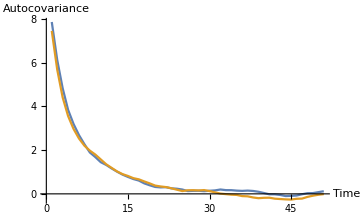

```mathematica
{engyA1,engyA2} =#["energy_sample"]&/@{a1Data,a2Data};

Row@{"Sample sizes: ",sampleSize=Length[engyA1]}
Assert[
sampleSize==Length[engyA2]
] 
(*{acrlAlg1 , acrlAlg2}= ListLinePlot[CovarianceFunction[#["energy_sample"], {50}], AxesLabel->{"Time", "Autocovariance"}, PlotRange->Full, ImageSize->Medium]& /@{a1Data, a2Data} ;
GraphicsColumn[{Labeled[acrlAlg1, "A1"], Labeled[acrlAlg2, "A2"]}, ImageSize->Large]*)

ListLinePlot[
CovarianceFunction[#["energy_sample"], {50}]& /@{a1Data, a2Data},
 AxesLabel->{"Time", "Autocovariance"}, PlotRange->Full, ImageSize->Medium]
```